# Using Machine Learning to Predict NBA Games

## By Elan Rotenberg Mentors: Etienne Bernard, Jerome Louradour

## Introduction

Predicting the winner of an NBA game, or any sports game for that matter, is a valuable resource for several reasons.  It allows one to make confident bets and earn money. It also allows analysts to determine which factors are most important to winning - perhaps helping teams out to win more games. A good percentage is seen as anywhere between 60-70%. Below are a few noteworthy companies with their accuracies across various NBA seasons.
	1.	FiveThirtyEight - one of the most revered sports analytics companies - correctly 			predicted the winner of 66.42% of games during the 2017-2018. 
	2.	NBA Miner predicted 65.3% of 2015-16 season correctly. 
	In this study, we plan to rival these numbers.

### Plan

There are many factors in an NBA game to consider from internal factors such as points, shots, rebounds, assists, passes, blocks, steals etc to external factors such as distance traveled to a game, elevation, home or road games, back to back games etc.
For this project, there were three groups of statistics that were considered
	1.	Rating System for each team
	Problems with winning percentage:
	Only based on wins and losses and not the quality of those wins and losses. May not 			accurately depict the skill of a team.
	Elo rating - a rating to measure the relative skill level of a team
	2.	External factors
	3.	Internal factors
		Box score statistics - these are common statistics that are easily available.

The following statistics were used in this project:
	1.	Elo rating
	2.	Location
	3.	Assists - moving average
	4.	Rebounds - moving average
	5.	Points - moving average
	6.	Free Throw Makes - moving average

The training set was created by collecting these statistics for all games between and including the 2008-09 and the 2017-18 seasons - 12,060 games. These statistics were then associated with either a “W” or “L”. A classifier was then run to predict the 2018-19 season.

### Import

The first step is to import the data.

```mathematica
ExternalEvaluate["Python","
from nba_api.stats.static import teams


"]
teams=ExternalEvaluate["Python","
from nba_api.stats.static import teams


teams.get_teams()
"];
seasons=ToString[#]<>"-"<>StringPadLeft[ToString[#-2000+1],2,"0"]&/@Range[2008,2018];
Bball=Table[Import[URLRead[<|"Scheme"->"https","User"->None,"Domain"->"stats.nba.com","Port"->None,"Path"->{"","stats","teamgamelog"},"Query"->{"DateFrom"->"","DateTo"->"","LeagueID"->"","Season"->season,"SeasonType"->"Regular Season","TeamID"->team},"Fragment"->None|>],"RawJSON"] ,{team,teams[[All,"id"]]},{season,seasons}];

bballstats=Table[Bball[[team,Season,3,1,3,game]],{team,30},{Season,11},{game,Length[Bball[[3,Season,3,1,3,All]]]}];
bballstatsc=Table[Reverse[bballstats[[m]][[n]]],{m,Length[bballstats]},{n,Length[bballstats[[m]]]}];
```

### Gather Stats

All desired stats are extracted and stored in an association.

```mathematica
seasonsAssoc=<||>;
Elos=<||>;

Table[
year=years;

bballstatsperyear=Table[bballstatsc[[team,years]],{team,30}];

findGame[date_]:=Cases[Flatten[bballstatsperyear,1],{___,date,___}];

bballDates=DeleteDuplicates[Table[Flatten[bballstatsperyear][[3+27a]],{a,Length[Flatten[bballstatsperyear]]/27.-1}]];

	bballDatesAbsolute=AbsoluteTime[bballDates[[#]]]&/@Range[Length[bballDates]];

		bballDatesChronological=Flatten[SortBy[Partition[Riffle[bballDates,bballDatesAbsolute],2],Last]][[#]]&/@Range[1,2*Length[bballDates],2];


bballStatsPerGame=Flatten[findGame[#]&/@bballDatesChronological,1];

	orderedBballStatsPerGame=SortBy[bballStatsPerGame,#[[2]]&];

							bballScoresPerGame=Partition[Table[{StringSplit[orderedBballStatsPerGame[[game,4]]][[1]],orderedBballStatsPerGame[[game,-1]]},{game,Length[orderedBballStatsPerGame]}],2];

		bballGamesNoDuplicates=orderedBballStatsPerGame[[;;;;2]];


bballHomeorAway=Table[If[StringSplit[bballGamesNoDuplicates[[a]][[4]]][[2]]=="vs.","HOME","AWAY"],{a,Length[bballGamesNoDuplicates]}];

bballWinorLoss=bballGamesNoDuplicates[[#]][[5]]&/@Range[Length[bballGamesNoDuplicates]];

teamNames=Sort[DeleteDuplicates[Select[Flatten[bballScoresPerGame],StringQ]]];



ELOS;

allElos={};

If[year==1,
Elos=<|#->1500&/@teamNames|>,
Elos=0.75*Elos+0.25*1505];

If[year==4,
AppendTo[Elos,"BKN"->Lookup[Elos,"NJN"]];
Delete[Elos,"NJN"]];

If[year==5,
AppendTo[Elos,"NOP"->Lookup[Elos,"NOH"]];
Delete[Elos,"NOH"]];


getElo[team_]:=Lookup[Elos,team];
Pwin[Elo1_, Elo2_] := 1/(1 + Power[10., -(Elo1-Elo2)/400]);
updateElo[game_] := Module[

{pwin, delta,flattened,team1,score1,team2,score2,Elo1,Elo2},

flattened=Flatten[game];
team1=flattened[[1]];
score1=flattened[[2]];
team2=flattened[[3]];
score2=flattened[[4]];
Elo1=getElo[team1];
Elo2=getElo[team2];
pwin = Pwin[Elo1, Elo2];


	If[score1 > score2,
		delta = 20*(1-pwin)
		,
		delta = -20*pwin;
		
	];
	
	{Elo1+delta, Elo2-delta};
AppendTo[Elos,<|team1->Elo1+delta,team2->Elo2-delta|>];
AppendTo[allElos,{Elo1,Elo2}]
];

updateElo[bballScoresPerGame[[#]]]&/@Range[Length[bballScoresPerGame]];



REBOUNDS;


Clear[getReb];
bballGames=Partition[Table[{StringSplit[orderedBballStatsPerGame[[game,4]]][[1]]},{game,Length[orderedBballStatsPerGame]}],2];
bballReboundsPerGame=Table[{StringSplit[orderedBballStatsPerGame[[game,4]]][[1]],orderedBballStatsPerGame[[game,-7]]},{game,Length[orderedBballStatsPerGame]}];
bballReboundsPerTeam=Table[Select[bballReboundsPerGame,#[[1]]==team&],{team,teamNames}];
ReboundsPerGame=Flatten[bballReboundsPerTeam[[#]]][[2;;;;2]]&/@Range[30];
movingAverageRebounds=Table[Mean[ReboundsPerGame[[team,1;;#]]]&/@Range[Length[ReboundsPerGame[[team]]]],{team,30}]//N;
movingAverageRebounds=PrependTo[movingAverageRebounds[[#]],0]&/@Range[30];
rebounds=Thread[teamNames->movingAverageRebounds];
getReb[team_]:=Lookup[rebounds,team];

allRebounds={};
updateRebound[game_]:=Module[
{flattened,team1,team2,rebound1,rebound2},

flattened=Flatten[game];
team1=flattened[[1]];
team2=flattened[[2]];
rebound1=getReb[team1];
rebound2=getReb[team2];

AppendTo[allRebounds,{rebound1[[1]],rebound2[[1]]}];
getReb[team1]=Drop[getReb[team1],1];
getReb[team2]=Drop[getReb[team2],1];
;
];
updateRebound[bballGames[[#]]]&/@Range[Length[bballGames]];
allRebounds;



ASSISTS;

Clear[getAss];
bballGames=Partition[Table[{StringSplit[orderedBballStatsPerGame[[game,4]]][[1]]},{game,Length[orderedBballStatsPerGame]}],2];
bballAssistsPerGame=Table[{StringSplit[orderedBballStatsPerGame[[game,4]]][[1]],orderedBballStatsPerGame[[game,-6]]},{game,Length[orderedBballStatsPerGame]}];
bballAssistsPerTeam=Table[Select[bballAssistsPerGame,#[[1]]==team&],{team,teamNames}];
AssistsPerGame=Flatten[bballAssistsPerTeam[[#]]][[2;;;;2]]&/@Range[30];
movingAverageAssists=Table[Mean[AssistsPerGame[[team,1;;#]]]&/@Range[Length[AssistsPerGame[[team]]]],{team,30}]//N;
movingAverageAssists=PrependTo[movingAverageAssists[[#]],0]&/@Range[30];
assists=Thread[teamNames->movingAverageAssists];
getAss[team_]:=Lookup[assists,team];

allAssists={};
updateAssists[game_]:=Module[
{flattened,team1,team2,rebound1,rebound2},

flattened=Flatten[game];
team1=flattened[[1]];
team2=flattened[[2]];
rebound1=getAss[team1];
rebound2=getAss[team2];

AppendTo[allAssists,{rebound1[[1]],rebound2[[1]]}];
getAss[team1]=Drop[getAss[team1],1];
getAss[team2]=Drop[getAss[team2],1];
;
];
updateAssists[bballGames[[#]]]&/@Range[Length[bballGames]];
allAssists;

FREE THROWS;

Clear[getFT];
bballGames=Partition[Table[{StringSplit[orderedBballStatsPerGame[[game,4]]][[1]]},{game,Length[orderedBballStatsPerGame]}],2];
bballFTPerGame=Table[{StringSplit[orderedBballStatsPerGame[[game,4]]][[1]],orderedBballStatsPerGame[[game,-12]]},{game,Length[orderedBballStatsPerGame]}];
bballFTPerTeam=Table[Select[bballFTPerGame,#[[1]]==team&],{team,teamNames}];
FTPerGame=Flatten[bballFTPerTeam[[#]]][[2;;;;2]]&/@Range[30];
movingAverageFT=Table[Mean[FTPerGame[[team,1;;#]]]&/@Range[Length[FTPerGame[[team]]]],{team,30}]//N;
movingAverageFT=PrependTo[movingAverageFT[[#]],0]&/@Range[30];
FT=Thread[teamNames->movingAverageFT];
getFT[team_]:=Lookup[FT,team];

allFT={};
updateFT[game_]:=Module[
{flattened,team1,team2,rebound1,rebound2},

flattened=Flatten[game];
team1=flattened[[1]];
team2=flattened[[2]];
rebound1=getFT[team1];
rebound2=getFT[team2];

AppendTo[allFT,{rebound1[[1]],rebound2[[1]]}];
getFT[team1]=Drop[getFT[team1],1];
getFT[team2]=Drop[getFT[team2],1];
;
];
updateFT[bballGames[[#]]]&/@Range[Length[bballGames]];
allFT;

POINTS PER GAME;

Clear[getPPG];
bballGames=Partition[Table[{StringSplit[orderedBballStatsPerGame[[game,4]]][[1]]},{game,Length[orderedBballStatsPerGame]}],2];
bballPPGPerGame=Table[{StringSplit[orderedBballStatsPerGame[[game,4]]][[1]],orderedBballStatsPerGame[[game,-1]]},{game,Length[orderedBballStatsPerGame]}];
bballPPGPerTeam=Table[Select[bballPPGPerGame,#[[1]]==team&],{team,teamNames}];
PPGPerGame=Flatten[bballPPGPerTeam[[#]]][[2;;;;2]]&/@Range[30];
movingAveragePPG=Table[Mean[PPGPerGame[[team,1;;#]]]&/@Range[Length[PPGPerGame[[team]]]],{team,30}]//N;
movingAveragePPG=PrependTo[movingAveragePPG[[#]],0]&/@Range[30];
PPG=Thread[teamNames->movingAveragePPG];
getPPG[team_]:=Lookup[PPG,team];

allPPG={};
updatePPG[game_]:=Module[
{flattened,team1,team2,rebound1,rebound2},

flattened=Flatten[game];
team1=flattened[[1]];
team2=flattened[[2]];
rebound1=getPPG[team1];
rebound2=getPPG[team2];

AppendTo[allPPG,{rebound1[[1]],rebound2[[1]]}];
getPPG[team1]=Drop[getPPG[team1],1];
getPPG[team2]=Drop[getPPG[team2],1];
;
];
updatePPG[bballGames[[#]]]&/@Range[Length[bballGames]];
allPPG;


SEASON ASSOCS;

elosHomeRebAssFTPPG=Partition[Flatten[Riffle[elosHomeRebAssFT,allPPG]],11];
	seasonsAssoc["season"<>ToString[years]<>"elosLocationGameRebAssFTPPG"]=Thread[elosHomeRebAssFTPPG->bballWinorLoss];

,
{years,11}];

seasonsAssoc2 = <||>;
Map[
	Function[seasonsAssoc2["season"<>ToString[#]] = seasonsAssoc["season"<>ToString[#]<>"elosLocationGameRebAssFT"]],
	Range[11]
];
```

### Testing

The method for testing the 2018-19 season (season 11) is as such:
Train season 10 and test season 11.
Train season 9,10 and test season 11.
This is completed until seasons 1 through 10 are trained and season 11 is tested.
The classifier will return different results every time. To combat this, we evaluate each training set combination ten times.

```mathematica
classifPerformances[train_, test_] := Map[
	Function @ ClassifierMeasurements[
		Classify[train,
			PerformanceGoal -> "Quality", RandomSeeding -> #, TimeGoal->Quantity[20, "Seconds"]
		],
		test
	]["Accuracy"],
	Range[10]
]
```

```mathematica
Table[
classifPerformances[Catenate[Values@Take[seasonsAssoc2,{-1-numSeasons,-2}]],seasonsAssoc2[[11]]],
{numSeasons,1,10}
]
```

### Results

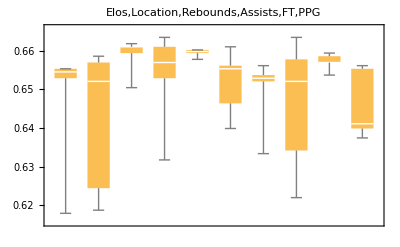

```mathematica
BoxWhiskerChart[eloLocationRebAssFTPPG,PlotLabel->Style["Elos,Location,Rebounds,Assists,FT,PPG",17,Black]]
```

We can easily strip one stat at a time using the functions below.

```mathematica
dropInputAt[input_,index_Integer] := dropInputAt[input, {index}]
dropInputAt[input_,index_List] := MapAt[Drop[#, index]&, input, 1]
seasonsEloLocationReboundsAssists=Map[dropInputAt[#,{8,9}]&,seasonsAssoc2,{2}];
```

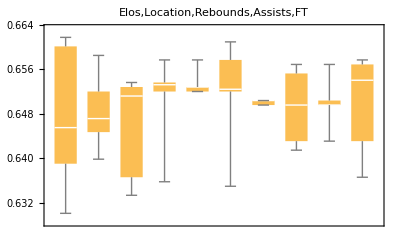

```mathematica
BoxWhiskerChart[eloLocationRebAssFT,PlotLabel->Style["Elos,Location,Rebounds,Assists,FT",17,Black]]
```

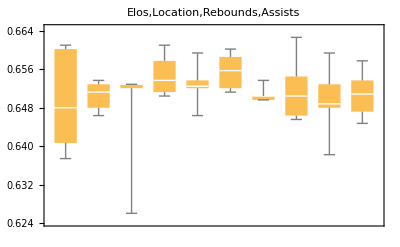

```mathematica
BoxWhiskerChart[eloLocationReboundsAssists,PlotLabel->Style["Elos,Location,Rebounds,Assists",17,Black]]
```

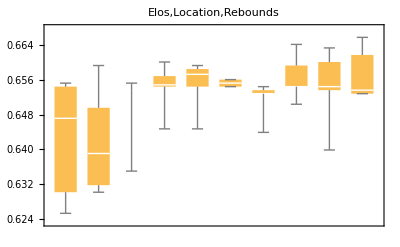

```mathematica
BoxWhiskerChart[eloLocationRebounds,PlotLabel->Style["Elos,Location,Rebounds",17,Black]]
```

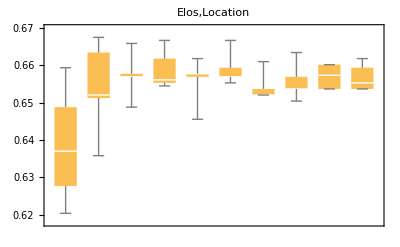

```mathematica
BoxWhiskerChart[eloLocation,PlotLabel->Style["Elos,Location",17,Black]]
```

```mathematica
averageFactor[factor1_,factor2_,factor3_,factor4_,factor5_]:=List[Mean@Mean@factor1,Mean@Mean@factor2,Mean@Mean@factor3,Mean@Mean@factor4,Mean@Mean@factor5]
```

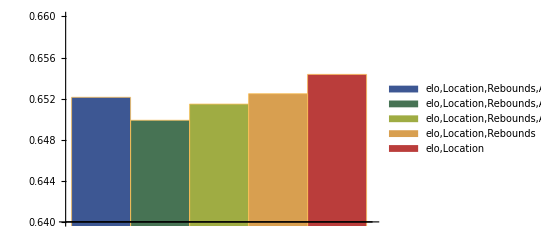

```mathematica
BarChart[averageFactor[eloLocationRebAssFTPPG,eloLocationRebAssFT,eloLocationReboundsAssists,eloLocationRebounds,eloLocation],ChartStyle->"DarkRainbow",BarSpacing->None,PlotRange->{{0.64,0.66}},ChartLegends->{"elo,Location,Rebounds,Assists,FT,PPG","elo,Location,Rebounds,Assists,FT","elo,Location,Rebounds,Assists","elo,Location,Rebounds","elo,Location"}]
```

The most accurate prediction of all of these options was actually the one with the least amount of variables - Elo and location.

```mathematica
averageFactor[eloLocation]
```

0.654358

This seems to indicate that Elo and location are the most important statistics in predicting the winner of a game.

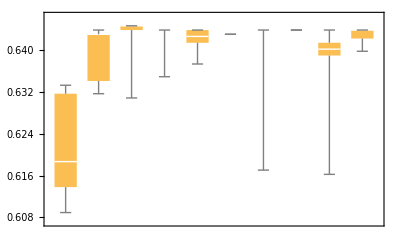

```mathematica
BoxWhiskerChart[elo]
```

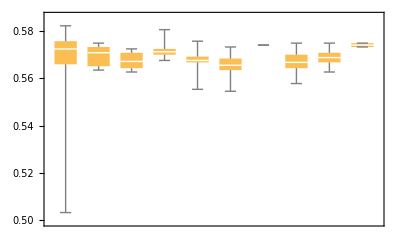

```mathematica
BoxWhiskerChart[PPGonly]
```

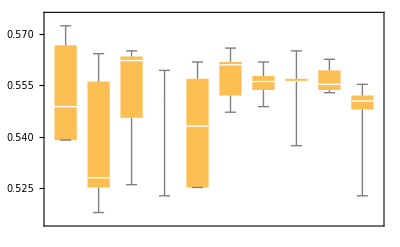

```mathematica
BoxWhiskerChart[assistsonly]
```

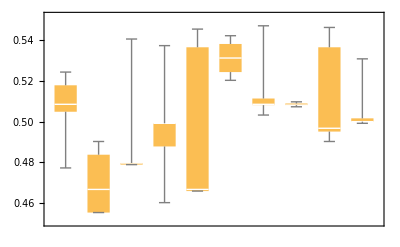

```mathematica
BoxWhiskerChart[reboundsonly]
```

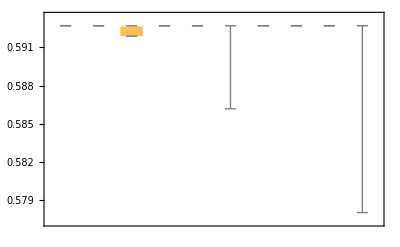

```mathematica
BoxWhiskerChart[locationonly]
```

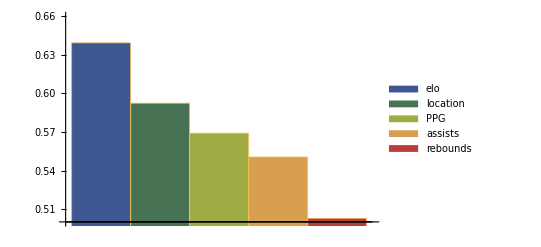

```mathematica
BarChart[{elo,location,PPG,assists,rebounds},ChartStyle->"DarkRainbow",BarSpacing->None,PlotRange->{{0.5,0.66}},ChartLegends->{"elo","location","PPG","assists","rebounds"}]
```

Elos is the most important factor, followed by location. All other statistics do not change the predictions much.

### Contact Information

Email: elan.rotenberg@gmail.com
LinkedIn: https://www.linkedin.com/in/elan-rotenberg-aa48b6115/